Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 6

Metoda sum skończonych

## Równanie Fredholma II rodzaju

### Zadanie

Metodą sum skończonych wyznaczyć rozwiązanie przybliżone równania:

y(x)=7/8 x-1/12+1/4∫_0^1 (x+t) y(t) ⅆt

Wykorzystać metodę trapezów.

Argument:  n

Wyznaczyć rozwiązanie dla n = 2, 4, 6, 8. 
Wykreślić błędy uzyskanych rozwiązań przybliżonych, gdy wiadomo, że rozwiązaniem dokładnym jest funkcja y(x)=x.

```mathematica
Clear[h];
Clear[mssf2];
mssf2[k_,f_,a_,b_,λ_,n_,z_Symbol]:=Module[{aa,aa1,aa2,aa3,h,yy,j,bb,ff,i,p,yp,xw},
h=(b-a)/n;
xw=Table[a+(i-1)*h,{i,1,n+1}];
aa=Table[h,{i,1,n+1}];
aa[[1]]*=1/2;
aa[[n+1]]*=1/2;
ff=Table[f[xw[[i]]],{i,1,n+1}];
bb=Table[KroneckerDelta[i,j]-λ*aa[[j]]*k[xw[[i]],xw[[j]]],{i,1,n+1},{j,1,n+1}];
yy=LinearSolve[bb,ff];
(*utworzenie rozwiązania przybliżonego*)
yp=f[z];
Do[yp+=λ*(aa[[j]]*k[z,xw[[j]]]*yy[[j]]),{j,1,n+1}];
(*wypisanie rozwiązania przybliżonego*)
Return[yp];
]
```

```mathematica
(* Funkcja 7/8 x-1/12+1/4∫_0^1 (x+t) y(t) ⅆt*)
k[x_,t_]:=(x+t);
f[x_]:= 7/8 x-1/12;
a=0;
b=1;
λ=1/4;
z = x;
```

```mathematica
(* n = {2,4,6,8} *)
n2 = mssf2[k,f,a,b,λ,2,z] //Simplify
n4 = mssf2[k,f,a,b,λ,4,z] //Simplify
n6 = mssf2[k,f,a,b,λ,6,z] //Simplify
n8 = mssf2[k,f,a,b,λ,8,z] //Simplify
```

1/570 (7+572 x)

(7+2288 x)/2286

(7+5148 x)/5146

(7+9152 x)/9150

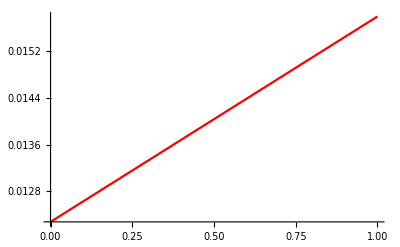

```mathematica
(* Błędy *)

plt1=Plot[Abs[n2-x],{x,0,1}, PlotStyle->Red];
plt2=Plot[Abs[n4-x],{x,0,1}, PlotStyle->Green];
plt3=Plot[Abs[n6-x],{x,0,1},  PlotStyle->Blue];
plt4=Plot[Abs[n8-x],{x,0,1}, PlotStyle->Yellow];
Show[plt1,plt2,plt3,plt4]
```